```mathematica
<<RiemannHilbert`
```

## Painleve

## NLS

```mathematica
λ=-1;
r[k_]:=0.5 Exp[-k^2];
cc[k_]:=Conjugate[k];
rb[k_]:=λ cc[r[cc[k]]];
```

```mathematica
θ[x_,t_][z_]:=2  (2 t z^2+x z);
```

```mathematica
G[x_,t_][z_]:=({{1+r[z]rb[z], rb[z]Exp[-2 I (2 t z^2+x z)]}, {r[z] Exp[2 I (2 t z^2+ x z)], 1}});
```

General::munfl: ArcTanh[2.83277×10^-16+1. ⅈ] is too small to represent as a normalized machine number; precision may be lost.

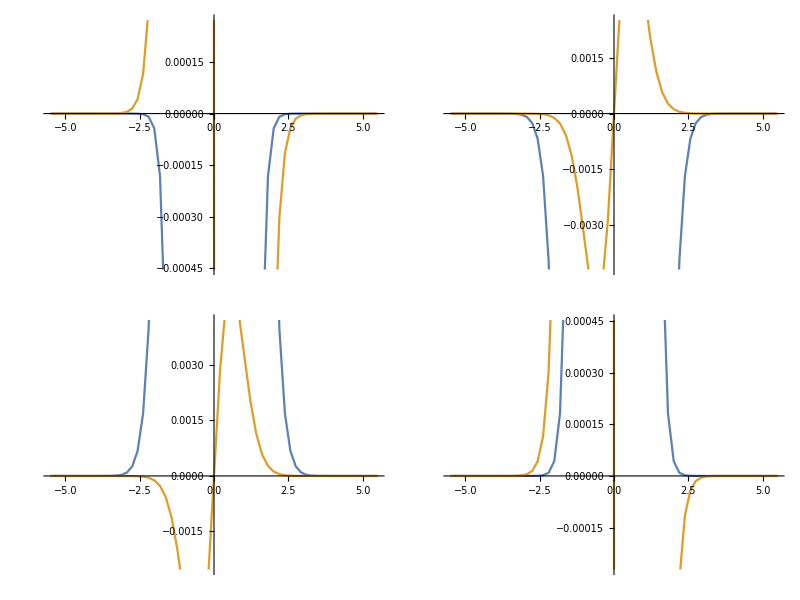
(-Graphics-)

```mathematica
V =Fun[G[0.0,0.0],Line[{-5.5,5.5}]]//RHSolve
```

```mathematica
{{1,0},{0,1}}+Cauchy[V,1+I]//ConsoleForm
```

```mathematica
{{0.9847854664616504-0.014938097892888065 ⅈ,-0.0778564768587141-0.05302708037085426 ⅈ},{0.07824233623082648+0.05395699475793745 ⅈ,1.0120649351483406+0.006873030868410332 ⅈ}}
```

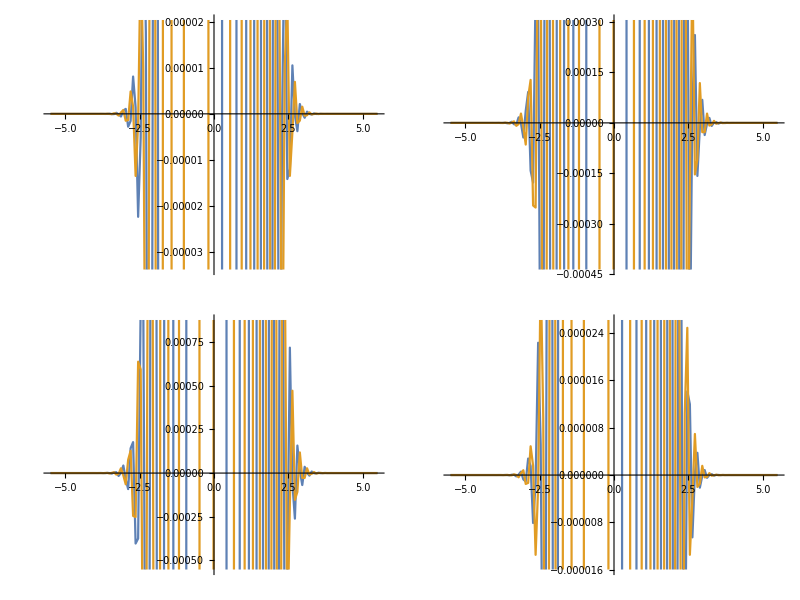
(-Graphics-)

```mathematica
V =Fun[G[1.0,1.0],Line[{-5.5,5.5}]]//RHSolve
```

```mathematica
V[0.1]
```

{{-0.124746-0.0140846 ⅈ,-0.510693+0.00146814 ⅈ},{0.510693+0.00146814 ⅈ,0.124746-0.0140846 ⅈ}}

```mathematica
I
```

ⅈ

```mathematica
G[0.0,0.0][-5.5]
```

{{1.,-3.64386×10^-14+0. ⅈ},{3.64386×10^-14+0. ⅈ,1}}